Program calculating bound states for dipole-dipole interaction for a given short-range phase
Everything in units of R_d and E_d (characteristic length and energy for dipole-dipole interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

Parameters:
β = (R_v/R_d)^4
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
xf -maximal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
emin - mimimal energy for bound state searching
emax - maximal energy for bound state searching
epsf - small number used to determine final point of integration
nptf - number of points to tabulate the final point of integration

```mathematica
Lmax=0;xi=0.2;xf=100;Id=IdentityMatrix[Lmax/2+1];nptl=200;npt=20;epsf=10^-3;epsi=10^-3;nptf=50;dxf=10;
freq=30000; 
freqz=0.1 freq;
d=9/(137*2);
m = 9.18 BohrM;
BohrM = 1.3996 (*MHz/Gauss*)
dp=0.5;
phimin =- N[π/2-0.01];
phimax=N[π/2-0.01];
```

1.3996

Conversion factor from Hz to Eh

```mathematica
HztoEh=1.519829 10^(-16);
```

Debye  in atomic units

```mathematica
Debye=0.393456;
```

Mass unit  in atomic units

```mathematica
massunit=1.661 10^(-24)/(9.110 10^(-28)); (*Unit/Masa elektronu*)
```

Parameters for Dy atoms

```mathematica
μ=81.25 massunit; (*Masa zredukowana*)
```

```mathematica
C6=2277;
```

```mathematica
Dperm=0.22 Debye;
```

Trap frequency and harm. osc. length

```mathematica
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6
(*ωz=2 π freqz HztoEh;aHOz=(1/Sqrt[μ ωz])/R6*)
```

9.52462

van der Waals length and energy

```mathematica
R6=(2 μ C6)^(1/4)
E6=1/(2 μ R6^2)
```

161.164

1.29946×10^-10

Characteristic length and energy for dipole-dipole interaction (vdw units)

```mathematica
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
R3
```

3.9669

3.9669

Harmonic oscillator energy in vdW units

```mathematica
α=(1/aHO)^4
αz=(1/aHOz)^4;
```

0.0121509

```mathematica
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz]
```

0.0220462

```mathematica
α=(Ω/2)^2;
αz=(Ωz/2)^2
```

0.000121509

Energy scale

```mathematica
emin=-0.001 Ωz ;emax=-20 Ωz;
```

Effective potential

```mathematica
Vdip[x_]:=π/aHO^3(2aHO Abs[x]-Sqrt[2π](aHO^2+x^2)Exp[x^2/(2 aHO^2)]Erfc[Abs[x]/(Sqrt[2]aHO)]);
```

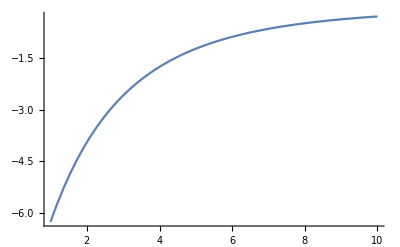

```mathematica
Plot[β Vdip[x],{x,1,10},PlotRange->All]
```

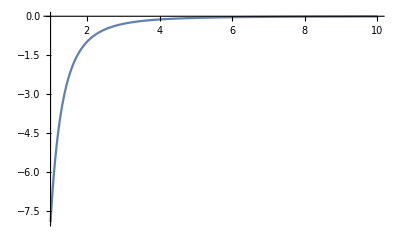

```mathematica
Plot[-(2β)/x^3,{x,1,10},PlotRange->All]
```

Mean scattering length of vdW potential  ????

```mathematica
abar=2 Pi/Gamma[1/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;aHO/abar
```

6.3013

Spherical Bessel functions  ????

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Potentials  !!!!!!

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
Veddtable[x_]:=N[(Table[Veddtab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
```

```mathematica
Vhotab//MatrixForm
Veddtab//MatrixForm
Vcftab//MatrixForm
Vvdwtab//MatrixForm
```

(1.00333)

(0.)

(0.)

(-1.)

```mathematica
αz
```

0.000121509

Matrix containg potential

```mathematica
V[x_]:= 1/x^6 Vvdwtab +β {Vdip[x]}+αz{ x^2} ;
```

```mathematica
V[1]//MatrixForm
Id//MatrixForm
ref ={-Ω};
refdiag = DiagonalMatrix[ref]//MatrixForm
```

(-7.25473)

(1)

(-0.220462)

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[l_,r_,phi_]=Sin[phi] Sqrt[r]BesselJ[1/4,1/(2 r^2)]+Cos[phi]Sqrt[r] BesselY[1/4,1/(2 r^2)];(*nie ma l*)
```

Table of short range solutions

```mathematica
Psi0[r_,ph_]:=Table[If[l1==l2,sol0[l1,r,ph],0] ,{l1,0,Lmax,2},{l2,0,Lmax,2}]
```

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

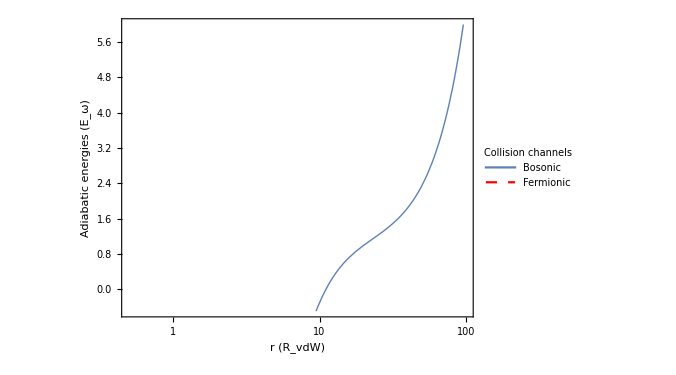

```mathematica
LogLinearPlot[{1/Ω(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]-ref),1/Ω(Take[Sort[Eigenvalues[V2[x]]],Lmax/2]-Take[ref,Lmax/2])},{x,0.5,xf},
PlotRange->{-0.5,6},AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

Subroutine determining final point of integration versus energy. This speeds up the numerical calculations. The plot shows final point of integration versus Log[10,-E]

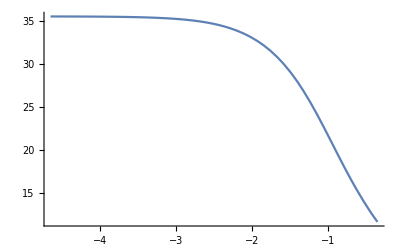

```mathematica
Module[{pemin,pemax,dp,TurnPoint,k,ExpInt,p,x,tabf},TurnPoint[e_?NumericQ]:=x/.FindRoot[e+1/x^6-αz x^2==0,{x,xi,xf}][[1]];
k[x_,e_]:=Sqrt[-(e+1/x^6-αz x^2)];
ExpInt[rf_?NumericQ,e_?NumericQ]:=NIntegrate[k[x,e],{x,TurnPoint[e],rf}];
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabf=Table[{p,x/.FindRoot[Exp[-ExpInt[x,-10^p]]==epsf,{x,TurnPoint[-10^p],xf}][[1]]},{p,pemin,pemax,(pemax-pemin)/nptf}];xfin=Interpolation[tabf];
Plot[xfin[x],{x,pemin,pemax}]]
```

Subroutine determining steps
Parameters:
npt -  number of points per one wave-lenght

InterpolatingFunction::dmval: Input value {0.100039} lies outside the range of data in the interpolating function. Extrapolation will be used.

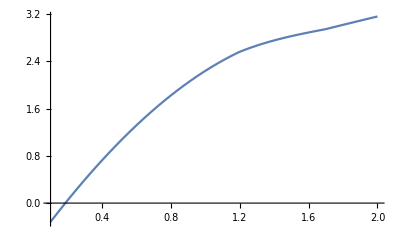

```mathematica
Module[{tab,eig,lambda,h,dbl,n},

tab=Table[eig=Eigenvalues[V[x]];{x,Min[Flatten[{2Pi/Sqrt[Abs[emin-eig]],2Pi/Sqrt[Abs[emax-eig]]}]]},{x,xi,xf,(xf-xi)/nptl}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,

AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
Plot[lambda[x],{x,0.1,2},PlotRange->All]
]
```

Number of steps

```mathematica
nstep
```

472

Matching point (somewhere between xi and xf in the classically allowed regime). It position is determined versus position of the classical turning point for highest L

```mathematica
xmid=x/.(FindRoot[V[x]-ref==emax,{x,xi,xf}])
```

6.95495

Location of the matching point in the table xt

```mathematica
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--
xt[[nmid]]
```

77

6.77779

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,phi_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ro},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],phi].Inverse[Psi0[xt[[n0]],phi]];
nodes+=Length[Select[Eigenvalues[Rout[n0]],#<0&]];(*Which functions change sign*)
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en + ref[[1]])Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
nodes+=Length[Select[Eigenvalues[Rout[n]],#<0&]];
n++;
];
Ro=Rout[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rout]];
{Ro,nodes}]
```

Subroutine performing inward integration using renormalized Noumerov method
It assumes that function vanishes at the starting value

Parameters:
Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumIn[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ri},

nodes=0;
h=xt[[n0-2]]-xt[[n0-1]];
W=Id+(h^2/12) QT[[n0-2]];
Rin[n0-1]=Inverse[W].(2 Id -(5h^2/6)QT[[n0-1]]);
nodes+=Length[Select[Eigenvalues[Rin[n0-1]],#<0&]];
n=n0-2;

While[n>=nf,
h0=h;
h=xt[[n-1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n+2]]).Inverse[Rin[n+1].Rin[n+2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en+ref[[1]]) Id-V[(xt[[n]]+xt[[n+1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n+1]]).Inverse[Rin[n+1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n+1]]).Inverse[Rin[n+1]]);
];
nodes+=Length[Select[Eigenvalues[Rin[n]],#<0&]];
n--;
];
Ri=Rin[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rin]];
{Ri,nodes}]
```

Subroutine calculating determinant that should vanish at the matching point if the energy is correct

Parameters:
en -  energy
phi -  short range phase

```mathematica
EigenEn[en_?NumericQ,phi_?NumericQ]:=
Module[{n,win,wout,nodes,det,m,nmax},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,1];  (* Performs outward integration *)
nodes=win[[2]]+wout[[2]]; (* Total number of nodes *) 
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[n,win,wout,QT];
{det,nodes,m}
]
```

```mathematica
Timing[EigenEn[-3.,Pi/4]]
```

InterpolatingFunction::dmval: Input value {0.477121} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.03125,{1.65995-Inverse[Rin[77]],4,{{1.65995-Inverse[Rin[77]]}}}}

```mathematica
detphi[ph_?NumericQ,en_?NumericQ]:=Module[{wout,m,det},
wout=evolNumOut[en,1,nmid,ph,1];
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[wout];
{det,m}]
```

Subroutine determining roots with the renormalized Noumerov method

Parameters:
en - energy of bound state
nst - 

Output:
tabsol -  table containing eigenenergies
tabm -  table of corresponding matrices that are used to dermine eigenvectors (null space vectors)

```mathematica
RootsF[en_?NumericQ,nst_?NumericQ]:=
Module[{nmax,tab,phi,n,xn,fn,tabR,tabsol,tabm,fun,x,tabv},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
tab=Table[{phi,detphi[phi,en]},{phi,phimin,phimax,Pi/nst}];
tabR={};
fun[x_?NumericQ]:=detphi[x,en][[1]];
For[n=1,n<Length[tab],n++,
If[(tab[[n,2,1]]tab[[n+1,2,1]]<=0),
xn=(tab[[n+1,1]]+tab[[n,1]])/2;
fn=fun[xn];
If[(tab[[n,2,1]]-fn)(tab[[n+1,2,1]]-fn)<0,AppendTo[tabR,{tab[[n,1]],tab[[n+1,1]]}]];
]
];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent",PrecisionGoal->9][[1]],{n,1,Length[tabR]}];
tabm=Table[detphi[tabsol[[n]],en][[2]],{n,1,Length[tabsol]}];
tabv=Table[NullSpace[tabm[[n]],Tolerance->10^-4][[1]],{n,1,Length[tabm]}];
Clear[tab,nmax,phi,n,xn,fn,tabR,fun,x,QT];
Print["tabsol=",tabsol];
{tabsol,tabv}]
```

```mathematica
RootsFOld[phi_?NumericQ,emn_?NumericQ,emx_?NumericQ]:=
Module[{tab,tabnew,tabR,pemin,pemax,dp=0.005,fun,tabsol,x,tabm,tabv},
pemin=Log[10,-emn];
pemax=Log[10,-emx];
tabnew=Table[{pen,EigenEn[-10^pen,phi]},{pen,pemin,pemax,dp}];
tabR={};
fun[x_?NumericQ]:=EigenEn[-10^x,phi][[1]];
Do[If[(tabnew[[n,2,1]]tabnew[[n+1,2,1]]<0)&&(tabnew[[n,2,2]]==tabnew[[n+1,2,2]]),AppendTo[tabR,{tabnew[[n,1]],tabnew[[n+1,1]]}]],{n,1,Length[tabnew]-1}];
tab=Table[{tabnew[[n,1]],tabnew[[n,2,1]]},{n,1,Length[tabnew]}];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent"][[1]],{n,1,Length[tabR]}];
tabm=Table[EigenEn[-10^tabsol[[n]],phi][[3]],{n,1,Length[tabsol]}];
{tabsol,tabm}]
```

```mathematica
ash[phi_]:=(Pi/8)(1+Tan[phi])/Gamma[5/4]^2
ϕ[a_]:=ArcTan[(8*Gamma[5/4]^2)/π a-1];
```

Subroutine calculating the wave function at the grid points in xt

Parameters:
phi - short-range phase
vec -  corerespondin eigenvector (value of the wave function at the matching point)

```mathematica
CalcPsi[phi_?NumericQ,en_?NumericQ,vecp_]:=Module[{win,wout,n,pe,nmax},
pe=Log[10,-en];
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[pe],nmax--];
win=evolNumIn[en,nmax,nmid+1,0]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,0];  (* Performs outward integration *)
Psi[nmid]=vecp;
Do[Psi[n]=Inverse[Rout[n]].Psi[n+1],{n,nmid-1,1,-1}];
Do[Psi[n]=Inverse[Rin[n]].Psi[n-1],{n,nmid+1,nmax-1}];
Psi[nmax]=0 Id.Psi[nmax-1];
Do[Psi[n]=0 Id.Psi[n-1];,{n,nmax+1,nstep}];
]
```

```mathematica
rts={};
dp=0.02;
Module[{pemin,pemax,pen,tabp,p},
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabp={};
p=pemin;
While[p≤pemax,AppendTo[tabp,p];p+=dp];
Print[tabp];
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[tabp]}]];
Do[en=-10^tabp[[i]];
k=i;
bound=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]==en,{x,0.2, 1000}]);
xf = 5bound;
xmid = xi+ (bound-xi)/2;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["en = ",en];*)
(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*);


AppendTo[rts, {-10^tabp[[i]],RootsF[-10^tabp[[i]],1000]}]

,{i,1,Length[tabp]}
]
]
```

{-4.65667,-4.63667,-4.61667,-4.59667,-4.57667,-4.55667,-4.53667,-4.51667,-4.49667,-4.47667,-4.45667,-4.43667,-4.41667,-4.39667,-4.37667,-4.35667,-4.33667,-4.31667,-4.29667,-4.27667,-4.25667,-4.23667,-4.21667,-4.19667,-4.17667,-4.15667,-4.13667,-4.11667,-4.09667,-4.07667,-4.05667,-4.03667,-4.01667,-3.99667,-3.97667,-3.95667,-3.93667,-3.91667,-3.89667,-3.87667,-3.85667,-3.83667,-3.81667,-3.79667,-3.77667,-3.75667,-3.73667,-3.71667,-3.69667,-3.67667,-3.65667,-3.63667,-3.61667,-3.59667,-3.57667,-3.55667,-3.53667,-3.51667,-3.49667,-3.47667,-3.45667,-3.43667,-3.41667,-3.39667,-3.37667,-3.35667,-3.33667,-3.31667,-3.29667,-3.27667,-3.25667,-3.23667,-3.21667,-3.19667,-3.17667,-3.15667,-3.13667,-3.11667,-3.09667,-3.07667,-3.05667,-3.03667,-3.01667,-2.99667,-2.97667,-2.95667,-2.93667,-2.91667,-2.89667,-2.87667,-2.85667,-2.83667,-2.81667,-2.79667,-2.77667,-2.75667,-2.73667,-2.71667,-2.69667,-2.67667,-2.65667,-2.63667,-2.61667,-2.59667,-2.57667,-2.55667,-2.53667,-2.51667,-2.49667,-2.47667,-2.45667,-2.43667,-2.41667,-2.39667,-2.37667,-2.35667,-2.33667,-2.31667,-2.29667,-2.27667,-2.25667,-2.23667,-2.21667,-2.19667,-2.17667,-2.15667,-2.13667,-2.11667,-2.09667,-2.07667,-2.05667,-2.03667,-2.01667,-1.99667,-1.97667,-1.95667,-1.93667,-1.91667,-1.89667,-1.87667,-1.85667,-1.83667,-1.81667,-1.79667,-1.77667,-1.75667,-1.73667,-1.71667,-1.69667,-1.67667,-1.65667,-1.63667,-1.61667,-1.59667,-1.57667,-1.55667,-1.53667,-1.51667,-1.49667,-1.47667,-1.45667,-1.43667,-1.41667,-1.39667,-1.37667,-1.35667,-1.33667,-1.31667,-1.29667,-1.27667,-1.25667,-1.23667,-1.21667,-1.19667,-1.17667,-1.15667,-1.13667,-1.11667,-1.09667,-1.07667,-1.05667,-1.03667,-1.01667,-0.996666,-0.976666,-0.956666,-0.936666,-0.916666,-0.896666,-0.876666,-0.856666,-0.836666,-0.816666,-0.796666,-0.776666,-0.756666,-0.736666,-0.716666,-0.696666,-0.676666,-0.656666,-0.636666,-0.616666,-0.596666,-0.576666,-0.556666,-0.536666,-0.516666,-0.496666,-0.476666,-0.456666,-0.436666,-0.416666,-0.396666,-0.376666,-0.356666}

Progress:

Part::partw: Part 1 of {} does not exist.

tabsol={-1.20138}

Part::partw: Part 1 of {} does not exist.

tabsol={-1.20139}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

tabsol={-1.2014}

tabsol={-1.20141}

tabsol={-1.20143}

tabsol={-1.20144}

tabsol={-1.20145}

tabsol={-1.20147}

tabsol={-1.20148}

tabsol={-1.20149}

tabsol={-1.20151}

tabsol={-1.20153}

tabsol={-1.20154}

tabsol={-1.20156}

tabsol={-1.20158}

tabsol={-1.2016}

tabsol={-1.20162}

tabsol={-1.20164}

tabsol={-1.20166}

tabsol={-1.20169}

tabsol={-1.20171}

tabsol={-1.20174}

tabsol={-1.20176}

tabsol={-1.20179}

tabsol={-1.20182}

tabsol={-1.20185}

tabsol={-1.20189}

tabsol={-1.20192}

tabsol={-1.20196}

tabsol={-1.20199}

tabsol={-1.20203}

tabsol={-1.20207}

tabsol={-1.20212}

tabsol={-1.20216}

tabsol={-1.20221}

tabsol={-1.20226}

tabsol={-1.20231}

tabsol={-1.20236}

tabsol={-1.20242}

tabsol={-1.20248}

tabsol={-1.20254}

tabsol={-1.2026}

tabsol={-1.20267}

tabsol={-1.20274}

tabsol={-1.20282}

tabsol={-1.2029}

tabsol={-1.20298}

tabsol={-1.20306}

tabsol={-1.20315}

tabsol={-1.20325}

tabsol={-1.20334}

tabsol={-1.20345}

tabsol={-1.20355}

tabsol={-1.20367}

tabsol={-1.20378}

tabsol={-1.20391}

tabsol={-1.20404}

tabsol={-1.20417}

tabsol={-1.20431}

tabsol={-1.20446}

tabsol={-1.20462}

tabsol={-1.20478}

tabsol={-1.20495}

tabsol={-1.20513}

tabsol={-1.20531}

tabsol={-1.20551}

tabsol={-1.20571}

tabsol={-1.20593}

tabsol={-1.20615}

tabsol={-1.20639}

tabsol={-1.20663}

tabsol={-1.20689}

tabsol={-1.20716}

tabsol={-1.20744}

tabsol={-1.20774}

tabsol={-1.20804}

tabsol={-1.20837}

tabsol={-1.20871}

tabsol={-1.20906}

tabsol={-1.20943}

tabsol={-1.20982}

tabsol={-1.21023}

tabsol={-1.21065}

tabsol={-1.2111}

tabsol={-1.21156}

tabsol={-1.21205}

tabsol={-1.21256}

tabsol={-1.2131}

tabsol={-1.21366}

tabsol={-1.21424}

tabsol={-1.21486}

tabsol={-1.2155}

tabsol={-1.21617}

tabsol={-1.21687}

tabsol={-1.21761}

tabsol={-1.21838}

tabsol={-1.21918}

tabsol={-1.22002}

tabsol={-1.22091}

tabsol={-1.22183}

tabsol={-1.2228}

tabsol={-1.22381}

tabsol={-1.22486}

tabsol={-1.22597}

tabsol={-1.22713}

tabsol={-1.22834}

tabsol={-1.2296}

tabsol={-1.23093}

tabsol={-1.23231}

tabsol={-1.23376}

tabsol={-1.23528}

tabsol={-1.23686}

tabsol={-1.23852}

tabsol={-1.24025}

tabsol={-1.24207}

tabsol={-1.24396}

tabsol={-1.24594}

tabsol={-1.24802}

tabsol={-1.25018}

tabsol={-1.25245}

tabsol={-1.25481}

tabsol={-1.25729}

tabsol={-1.25987}

tabsol={-1.26257}

tabsol={-1.26539}

tabsol={-1.26834}

tabsol={-1.27142}

tabsol={-1.27464}

tabsol={-1.278}

tabsol={-1.2815}

tabsol={-1.28517}

tabsol={-1.28899}

tabsol={-1.29299}

tabsol={-1.29715}

tabsol={-1.3015}

tabsol={-1.30604}

tabsol={-1.31078}

tabsol={-1.31572}

tabsol={-1.32087}

tabsol={-1.32624}

tabsol={-1.33184}

tabsol={-1.33768}

tabsol={-1.34377}

tabsol={-1.35012}

tabsol={-1.35673}

tabsol={-1.36361}

tabsol={-1.37078}

tabsol={-1.37825}

tabsol={-1.38602}

tabsol={-1.39411}

tabsol={-1.40254}

tabsol={-1.4113}

tabsol={-1.42041}

tabsol={-1.42988}

tabsol={-1.43974}

tabsol={-1.44998}

tabsol={-1.46062}

tabsol={-1.47168}

tabsol={-1.48316}

tabsol={-1.49509}

tabsol={-1.50748}

tabsol={-1.52033}

tabsol={-1.53367}

tabsol={-1.54752}

tabsol={}

tabsol={}

tabsol={1.54936}

tabsol={1.53333}

tabsol={1.51672}

tabsol={1.4995}

tabsol={1.48164}

tabsol={1.46313}

tabsol={1.44393}

tabsol={1.42404}

tabsol={1.40341}

tabsol={1.38201}

tabsol={1.35982}

tabsol={1.3368}

tabsol={1.31291}

tabsol={1.28811}

tabsol={1.26235}

tabsol={1.23557}

tabsol={1.20773}

tabsol={1.17875}

tabsol={1.14857}

tabsol={1.11712}

tabsol={1.08429}

tabsol={1.05}

tabsol={1.01414}

tabsol={0.976581}

tabsol={0.9372}

tabsol={0.895843}

tabsol={0.852349}

tabsol={0.806537}

tabsol={0.75821}

tabsol={0.707155}

tabsol={0.653143}

tabsol={0.595935}

tabsol={0.535281}

tabsol={0.470757}

tabsol={0.402492}

tabsol={0.330091}

tabsol={0.253392}

tabsol={0.172303}

tabsol={0.0868331}

tabsol={-0.00288431}

tabsol={-0.0965654}

tabsol={-0.193763}

tabsol={-0.293872}

tabsol={}

tabsol={}

tabsol={-0.601229}

tabsol={-0.705709}

tabsol={-0.81359}

tabsol={-0.911329}

tabsol={-1.00724}

```mathematica
taben={};tabphi={};tabvec={};
Do[AppendTo[taben,{aHOz/ash[rts[[n,2,1,m]]],1/Ωz rts[[n,1]]}];AppendTo[tabphi,{rts[[n,2,1,m]],rts[[n,1]]}];AppendTo[tabvec,rts[[n,2,2,m]]],{n,1,Length[rts]},{m,1,Length[rts[[n,2,1]]]}];
```

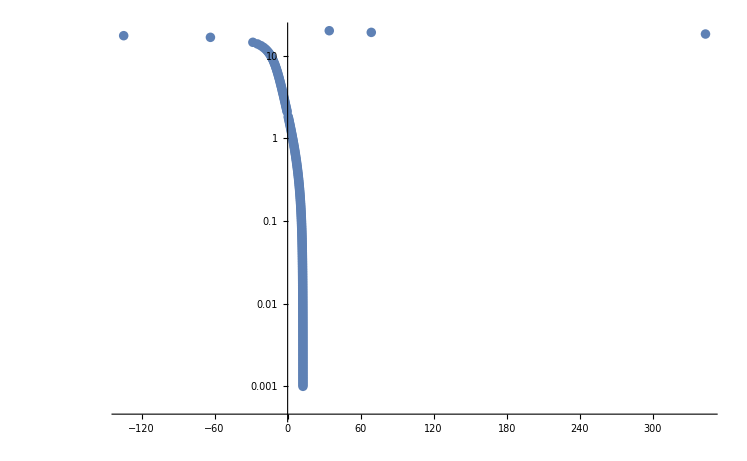

{{-12.59,-0.001},{-12.5894,-0.00104713},{-12.5888,-0.00109648},{-12.5881,-0.00114815},{-12.5873,-0.00120226},{-12.5866,-0.00125893},{-12.5858,-0.00131826},{-12.585,-0.00138038},{-12.5841,-0.00144544},{-12.5832,-0.00151356},{-12.5823,-0.00158489},{-12.5813,-0.00165959},{-12.5802,-0.0017378},{-12.5791,-0.0018197},{-12.578,-0.00190546},{-12.5768,-0.00199526},{-12.5755,-0.0020893},{-12.5742,-0.00218776},{-12.5729,-0.00229087},{-12.5714,-0.00239883},{-12.5699,-0.00251189},{-12.5684,-0.00263027},{-12.5667,-0.00275423},{-12.565,-0.00288403},{-12.5632,-0.00301995},{-12.5613,-0.00316228},{-12.5593,-0.00331131},{-12.5572,-0.00346737},{-12.5551,-0.00363078},{-12.5528,-0.00380189},{-12.5504,-0.00398107},{-12.5479,-0.00416869},{-12.5453,-0.00436516},{-12.5426,-0.00457088},{-12.5398,-0.0047863},{-12.5368,-0.00501187},{-12.5336,-0.00524807},{-12.5304,-0.00549541},{-12.5269,-0.0057544},{-12.5233,-0.0060256},{-12.5196,-0.00630957},{-12.5157,-0.00660693},{-12.5115,-0.00691831},{-12.5072,-0.00724436},{-12.5027,-0.00758578},{-12.498,-0.00794328},{-12.4931,-0.00831764},{-12.4879,-0.00870964},{-12.4825,-0.00912011},{-12.4768,-0.00954993},{-12.4709,-0.01},{-12.4647,-0.0104713},{-12.4582,-0.0109648},{-12.4514,-0.0114815},{-12.4443,-0.0120226},{-12.4368,-0.0125893},{-12.429,-0.0131826},{-12.4209,-0.0138038},{-12.4123,-0.0144544},{-12.4034,-0.0151356},{-12.3941,-0.0158489},{-12.3843,-0.0165959},{-12.3741,-0.017378},{-12.3634,-0.018197},{-12.3522,-0.0190546},{-12.3405,-0.0199526},{-12.3283,-0.020893},{-12.3155,-0.0218776},{-12.3021,-0.0229087},{-12.2881,-0.0239883},{-12.2734,-0.0251189},{-12.2581,-0.0263027},{-12.2421,-0.0275423},{-12.2254,-0.0288403},{-12.2079,-0.0301995},{-12.1896,-0.0316228},{-12.1704,-0.0331131},{-12.1504,-0.0346737},{-12.1295,-0.0363078},{-12.1077,-0.0380189},{-12.0848,-0.0398107},{-12.061,-0.0416869},{-12.036,-0.0436516},{-12.01,-0.0457088},{-11.9828,-0.047863},{-11.9544,-0.0501187},{-11.9247,-0.0524807},{-11.8937,-0.0549541},{-11.8613,-0.057544},{-11.8275,-0.060256},{-11.7922,-0.0630957},{-11.7554,-0.0660693},{-11.717,-0.0691831},{-11.6769,-0.0724436},{-11.6351,-0.0758578},{-11.5914,-0.0794328},{-11.5459,-0.0831764},{-11.4985,-0.0870964},{-11.449,-0.0912011},{-11.3975,-0.0954993},{-11.3437,-0.1},{-11.2877,-0.104713},{-11.2294,-0.109648},{-11.1687,-0.114815},{-11.1055,-0.120226},{-11.0396,-0.125893},{-10.9711,-0.131826},{-10.8999,-0.138038},{-10.8258,-0.144544},{-10.7487,-0.151356},{-10.6686,-0.158489},{-10.5853,-0.165959},{-10.4988,-0.17378},{-10.409,-0.18197},{-10.3158,-0.190546},{-10.2191,-0.199526},{-10.1187,-0.20893},{-10.0146,-0.218776},{-9.90676,-0.229087},{-9.795,-0.239883},{-9.67925,-0.251189},{-9.55942,-0.263027},{-9.43544,-0.275423},{-9.3072,-0.288403},{-9.17464,-0.301995},{-9.03767,-0.316228},{-8.89622,-0.331131},{-8.75023,-0.346737},{-8.59962,-0.363078},{-8.44433,-0.380189},{-8.28433,-0.398107},{-8.11954,-0.416869},{-7.94995,-0.436516},{-7.7755,-0.457088},{-7.59619,-0.47863},{-7.41198,-0.501187},{-7.22287,-0.524807},{-7.02886,-0.549541},{-6.82996,-0.57544},{-6.62619,-0.60256},{-6.41756,-0.630957},{-6.20413,-0.660693},{-5.98593,-0.691831},{-5.76302,-0.724436},{-5.53547,-0.758578},{-5.30335,-0.794328},{-5.06674,-0.831764},{-4.82575,-0.870964},{-4.58046,-0.912011},{-4.331,-0.954993},{-4.07749,-1.},{-3.82003,-1.04713},{-3.55878,-1.09648},{-3.29386,-1.14815},{-3.02542,-1.20226},{-2.7536,-1.25893},{-2.47855,-1.31826},{-2.20041,-1.38038},{-1.91934,-1.44544},{-1.63548,-1.51356},{-1.34898,-1.58489},{-1.05997,-1.65959},{-0.768592,-1.7378},{-0.474967,-1.8197},{0.418278,-2.0893},{0.719843,-2.18776},{1.0232,-2.29087},{1.32831,-2.39883},{1.63515,-2.51189},{1.94373,-2.63027},{2.25407,-2.75423},{2.56623,-2.88403},{2.8803,-3.01995},{3.19641,-3.16228},{3.51472,-3.31131},{3.83544,-3.46737},{4.15882,-3.63078},{4.48517,-3.80189},{4.81486,-3.98107},{5.14831,-4.16869},{5.48607,-4.36516},{5.82869,-4.57088},{6.17688,-4.7863},{6.53145,-5.01187},{6.89333,-5.24807},{7.26364,-5.49541},{7.64366,-5.7544},{8.03487,-6.0256},{8.43907,-6.30957},{8.85834,-6.60693},{9.29518,-6.91831},{9.75259,-7.24436},{10.2342,-7.58578},{10.7444,-7.94328},{11.2887,-8.31764},{11.8738,-8.70964},{12.5085,-9.12011},{13.2058,-9.54993},{13.9763,-10.},{14.8414,-10.4713},{15.8277,-10.9648},{16.9727,-11.4815},{18.3307,-12.0226},{19.9841,-12.5893},{22.0637,-13.1826},{24.7911,-13.8038},{28.5739,-14.4544},{63.4485,-16.5959},{134.724,-17.378},{-343.356,-18.197},{-68.7348,-19.0546},{-34.2089,-19.9526}}

```mathematica
ListLogPlot[-taben,PlotRange->All]
taben
```

```mathematica
emin = -emin; emax = -emax;
```

```mathematica
rts1={};
Module[{pemin,pemax,pen,tabe,p},
tabe={};
dp=0.002 emax;
p=emin;
While[p≤emax,AppendTo[tabe,p];p+=dp];
Print[tabe];
Print["Progress:"];
Print[ProgressIndicator[Dynamic[n],{1,Length[tabe]}]];
Do[en=tabe[[i]];
n=i;

bound=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]==en,{x,0.2, 1000}]);
xf = 5bound;
xmid = xi+ (bound-xi)/2;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;
(*Print["en = ",en];
Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts1, {tabe[[i]],RootsF[tabe[[i]],500]}]

,{i,1,Length[tabe]}
]
]
```

{0.0000220462,0.000903895,0.00178574,0.00266759,0.00354944,0.00443129,0.00531314,0.00619499,0.00707684,0.00795869,0.00884054,0.00972239,0.0106042,0.0114861,0.0123679,0.0132498,0.0141316,0.0150135,0.0158953,0.0167772,0.017659,0.0185409,0.0194227,0.0203046,0.0211864,0.0220683,0.0229501,0.023832,0.0247138,0.0255957,0.0264775,0.0273594,0.0282412,0.0291231,0.0300049,0.0308868,0.0317686,0.0326505,0.0335323,0.0344142,0.035296,0.0361779,0.0370597,0.0379416,0.0388234,0.0397053,0.0405871,0.041469,0.0423508,0.0432327,0.0441145,0.0449964,0.0458782,0.04676,0.0476419,0.0485237,0.0494056,0.0502874,0.0511693,0.0520511,0.052933,0.0538148,0.0546967,0.0555785,0.0564604,0.0573422,0.0582241,0.0591059,0.0599878,0.0608696,0.0617515,0.0626333,0.0635152,0.064397,0.0652789,0.0661607,0.0670426,0.0679244,0.0688063,0.0696881,0.07057,0.0714518,0.0723337,0.0732155,0.0740974,0.0749792,0.0758611,0.0767429,0.0776248,0.0785066,0.0793885,0.0802703,0.0811522,0.082034,0.0829159,0.0837977,0.0846796,0.0855614,0.0864433,0.0873251,0.088207,0.0890888,0.0899707,0.0908525,0.0917344,0.0926162,0.0934981,0.0943799,0.0952618,0.0961436,0.0970254,0.0979073,0.0987891,0.099671,0.100553,0.101435,0.102317,0.103198,0.10408,0.104962,0.105844,0.106726,0.107608,0.108489,0.109371,0.110253,0.111135,0.112017,0.112899,0.113781,0.114662,0.115544,0.116426,0.117308,0.11819,0.119072,0.119954,0.120835,0.121717,0.122599,0.123481,0.124363,0.125245,0.126126,0.127008,0.12789,0.128772,0.129654,0.130536,0.131418,0.132299,0.133181,0.134063,0.134945,0.135827,0.136709,0.137591,0.138472,0.139354,0.140236,0.141118,0.142,0.142882,0.143763,0.144645,0.145527,0.146409,0.147291,0.148173,0.149055,0.149936,0.150818,0.1517,0.152582,0.153464,0.154346,0.155227,0.156109,0.156991,0.157873,0.158755,0.159637,0.160519,0.1614,0.162282,0.163164,0.164046,0.164928,0.16581,0.166692,0.167573,0.168455,0.169337,0.170219,0.171101,0.171983,0.172864,0.173746,0.174628,0.17551,0.176392,0.177274,0.178156,0.179037,0.179919,0.180801,0.181683,0.182565,0.183447,0.184329,0.18521,0.186092,0.186974,0.187856,0.188738,0.18962,0.190501,0.191383,0.192265,0.193147,0.194029,0.194911,0.195793,0.196674,0.197556,0.198438,0.19932,0.200202,0.201084,0.201965,0.202847,0.203729,0.204611,0.205493,0.206375,0.207257,0.208138,0.20902,0.209902,0.210784,0.211666,0.212548,0.21343,0.214311,0.215193,0.216075,0.216957,0.217839,0.218721,0.219602,0.220484,0.221366,0.222248,0.22313,0.224012,0.224894,0.225775,0.226657,0.227539,0.228421,0.229303,0.230185,0.231067,0.231948,0.23283,0.233712,0.234594,0.235476,0.236358,0.237239,0.238121,0.239003,0.239885,0.240767,0.241649,0.242531,0.243412,0.244294,0.245176,0.246058,0.24694,0.247822,0.248703,0.249585,0.250467,0.251349,0.252231,0.253113,0.253995,0.254876,0.255758,0.25664,0.257522,0.258404,0.259286,0.260168,0.261049,0.261931,0.262813,0.263695,0.264577,0.265459,0.26634,0.267222,0.268104,0.268986,0.269868,0.27075,0.271632,0.272513,0.273395,0.274277,0.275159,0.276041,0.276923,0.277805,0.278686,0.279568,0.28045,0.281332,0.282214,0.283096,0.283977,0.284859,0.285741,0.286623,0.287505,0.288387,0.289269,0.29015,0.291032,0.291914,0.292796,0.293678,0.29456,0.295442,0.296323,0.297205,0.298087,0.298969,0.299851,0.300733,0.301614,0.302496,0.303378,0.30426,0.305142,0.306024,0.306906,0.307787,0.308669,0.309551,0.310433,0.311315,0.312197,0.313078,0.31396,0.314842,0.315724,0.316606,0.317488,0.31837,0.319251,0.320133,0.321015,0.321897,0.322779,0.323661,0.324543,0.325424,0.326306,0.327188,0.32807,0.328952,0.329834,0.330715,0.331597,0.332479,0.333361,0.334243,0.335125,0.336007,0.336888,0.33777,0.338652,0.339534,0.340416,0.341298,0.34218,0.343061,0.343943,0.344825,0.345707,0.346589,0.347471,0.348352,0.349234,0.350116,0.350998,0.35188,0.352762,0.353644,0.354525,0.355407,0.356289,0.357171,0.358053,0.358935,0.359816,0.360698,0.36158,0.362462,0.363344,0.364226,0.365108,0.365989,0.366871,0.367753,0.368635,0.369517,0.370399,0.371281,0.372162,0.373044,0.373926,0.374808,0.37569,0.376572,0.377453,0.378335,0.379217,0.380099,0.380981,0.381863,0.382745,0.383626,0.384508,0.38539,0.386272,0.387154,0.388036,0.388918,0.389799,0.390681,0.391563,0.392445,0.393327,0.394209,0.39509,0.395972,0.396854,0.397736,0.398618,0.3995,0.400382,0.401263,0.402145,0.403027,0.403909,0.404791,0.405673,0.406554,0.407436,0.408318,0.4092,0.410082,0.410964,0.411846,0.412727,0.413609,0.414491,0.415373,0.416255,0.417137,0.418019,0.4189,0.419782,0.420664,0.421546,0.422428,0.42331,0.424191,0.425073,0.425955,0.426837,0.427719,0.428601,0.429483,0.430364,0.431246,0.432128,0.43301,0.433892,0.434774,0.435656,0.436537,0.437419,0.438301,0.439183,0.440065}

Progress:

Part::partw: Part 1 of {} does not exist.

tabsol={-1.20095}

Part::partw: Part 1 of {} does not exist.

tabsol={-1.19219}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

tabsol={-1.18337}

tabsol={-1.17449}

tabsol={-1.16554}

tabsol={-1.15653}

tabsol={-1.14746}

tabsol={-1.13832}

tabsol={-1.12912}

tabsol={-1.11985}

tabsol={-1.11051}

tabsol={-1.10111}

tabsol={-1.09163}

tabsol={-1.08209}

tabsol={-1.07247}

tabsol={-1.06278}

tabsol={-1.05302}

tabsol={-1.04319}

tabsol={-1.03328}

tabsol={-1.0233}

tabsol={-1.01344}

tabsol={-1.00331}

tabsol={-0.993102}

tabsol={-0.982815}

tabsol={-0.972448}

tabsol={-0.962003}

tabsol={-0.951477}

tabsol={-0.940871}

tabsol={-0.930183}

tabsol={-0.919413}

tabsol={-0.90856}

tabsol={-0.897624}

tabsol={-0.886604}

tabsol={-0.875499}

tabsol={-0.864309}

tabsol={-0.853033}

tabsol={-0.841672}

tabsol={-0.830223}

tabsol={-0.818688}

tabsol={-0.807065}

tabsol={-0.795354}

tabsol={-0.783555}

tabsol={-0.771668}

tabsol={-0.759692}

tabsol={-0.747627}

tabsol={-0.735473}

tabsol={-0.72323}

tabsol={-0.710897}

tabsol={-0.698476}

tabsol={-0.685806}

tabsol={-0.673204}

tabsol={-0.660513}

tabsol={-0.647733}

tabsol={-0.634864}

tabsol={-0.621907}

tabsol={-0.608862}

tabsol={-0.595729}

tabsol={-0.58251}

tabsol={-0.569204}

tabsol={-0.555812}

tabsol={-0.542334}

tabsol={-0.528773}

tabsol={-0.515127}

tabsol={-0.501399}

tabsol={-0.48759}

tabsol={-0.473699}

tabsol={-0.459729}

tabsol={-0.44568}

tabsol={-0.431554}

tabsol={-0.417353}

tabsol={-0.403077}

tabsol={-0.388727}

tabsol={-0.374307}

tabsol={-0.359816}

tabsol={-0.345257}

tabsol={-0.330632}

tabsol={-0.315942}

tabsol={-0.301189}

tabsol={-0.286375}

tabsol={-0.271502}

tabsol={-0.256573}

tabsol={-0.241588}

tabsol={-0.226551}

tabsol={-0.211464}

tabsol={-0.196328}

tabsol={-0.181146}

tabsol={-0.16592}

tabsol={-0.150654}

tabsol={-0.135348}

tabsol={-0.120006}

tabsol={-0.10463}

tabsol={-0.0892224}

tabsol={-0.0737856}

tabsol={-0.0583223}

tabsol={-0.0428348}

tabsol={-0.0273256}

tabsol={-0.0117974}

tabsol={0.00374755}

tabsol={0.0193066}

tabsol={0.0348775}

tabsol={0.0504576}

tabsol={0.0660445}

tabsol={0.0816359}

tabsol={0.0972295}

tabsol={0.112823}

tabsol={0.128414}

tabsol={0.144}

tabsol={0.159579}

tabsol={0.17515}

tabsol={0.190709}

tabsol={0.206255}

tabsol={0.221786}

tabsol={0.237301}

tabsol={0.252796}

tabsol={0.268271}

tabsol={0.283724}

tabsol={0.299154}

tabsol={0.314558}

tabsol={0.329935}

tabsol={0.345285}

tabsol={0.360605}

tabsol={0.375895}

tabsol={0.391153}

tabsol={0.406379}

tabsol={0.421571}

tabsol={0.436729}

tabsol={0.451852}

tabsol={0.46694}

tabsol={0.481991}

tabsol={0.497006}

tabsol={0.511984}

tabsol={0.526924}

tabsol={0.541827}

tabsol={0.556692}

tabsol={0.57152}

tabsol={0.586311}

tabsol={0.601064}

tabsol={0.615779}

tabsol={0.630459}

tabsol={0.645102}

tabsol={0.659709}

tabsol={0.674281}

tabsol={0.688818}

tabsol={0.703322}

tabsol={0.717793}

tabsol={0.732232}

tabsol={0.74664}

tabsol={0.761018}

tabsol={0.775367}

tabsol={0.789689}

tabsol={0.803985}

tabsol={0.818257}

tabsol={0.832505}

tabsol={0.846731}

tabsol={0.860937}

tabsol={0.875125}

tabsol={0.889297}

tabsol={0.903453}

tabsol={0.917597}

tabsol={0.93173}

tabsol={0.945855}

tabsol={0.959973}

tabsol={0.974086}

tabsol={0.988198}

tabsol={1.00231}

tabsol={1.01642}

tabsol={1.03054}

tabsol={1.04467}

tabsol={1.05881}

tabsol={1.07296}

tabsol={1.08713}

tabsol={1.10132}

tabsol={1.11553}

tabsol={1.12976}

tabsol={1.14403}

tabsol={1.15832}

tabsol={1.17266}

tabsol={1.18703}

tabsol={1.20144}

tabsol={1.21589}

tabsol={1.2304}

tabsol={1.24496}

tabsol={1.25958}

tabsol={1.27426}

tabsol={1.28901}

tabsol={1.30383}

tabsol={1.31872}

tabsol={1.33369}

tabsol={1.34874}

tabsol={1.36389}

tabsol={1.37913}

tabsol={1.39446}

tabsol={1.40991}

tabsol={1.42546}

tabsol={1.44112}

tabsol={1.45691}

tabsol={1.47283}

tabsol={1.48888}

tabsol={1.50507}

tabsol={1.5214}

tabsol={1.53789}

tabsol={1.55454}

tabsol={}

tabsol={-1.55325}

tabsol={-1.53608}

tabsol={-1.51872}

tabsol={-1.50117}

tabsol={-1.48341}

tabsol={-1.46543}

tabsol={-1.44724}

tabsol={-1.42881}

tabsol={-1.41014}

tabsol={-1.39123}

tabsol={-1.37205}

tabsol={-1.35261}

tabsol={-1.33289}

tabsol={-1.31288}

tabsol={-1.29258}

tabsol={-1.27197}

tabsol={-1.25104}

tabsol={-1.22978}

tabsol={-1.20818}

tabsol={-1.18623}

tabsol={-1.16392}

tabsol={-1.14124}

tabsol={-1.11818}

tabsol={-1.09473}

tabsol={-1.07088}

tabsol={-1.04661}

tabsol={-1.02192}

tabsol={-0.996804}

tabsol={-0.971247}

tabsol={-0.945242}

tabsol={-0.918783}

tabsol={-0.891864}

tabsol={-0.864477}

tabsol={-0.83662}

tabsol={-0.808288}

tabsol={-0.77948}

tabsol={-0.750195}

tabsol={-0.720434}

tabsol={-0.6902}

tabsol={-0.659498}

tabsol={-0.628333}

tabsol={-0.596714}

tabsol={-0.564652}

tabsol={-0.53216}

tabsol={-0.499252}

tabsol={-0.465947}

tabsol={-0.432262}

tabsol={-0.398222}

tabsol={-0.363848}

tabsol={-0.329167}

tabsol={-0.294207}

tabsol={-0.258997}

tabsol={-0.223569}

tabsol={-0.187954}

tabsol={-0.152186}

tabsol={-0.116298}

tabsol={-0.0803249}

tabsol={-0.0443014}

tabsol={-0.0082614}

tabsol={0.0277614}

tabsol={0.0637343}

tabsol={0.0996257}

tabsol={0.135405}

tabsol={0.171044}

tabsol={0.206517}

tabsol={0.241797}

tabsol={0.276864}

tabsol={0.311696}

tabsol={0.346277}

tabsol={0.380591}

tabsol={0.414624}

tabsol={0.448369}

tabsol={0.481815}

tabsol={0.514958}

tabsol={0.547795}

tabsol={0.580324}

tabsol={0.612548}

tabsol={0.644468}

tabsol={0.676091}

tabsol={0.707423}

tabsol={0.738473}

tabsol={0.76925}

tabsol={0.799767}

tabsol={0.830036}

tabsol={0.860071}

tabsol={0.889888}

tabsol={0.919502}

tabsol={0.948932}

tabsol={0.978195}

tabsol={1.00731}

tabsol={1.0363}

tabsol={1.06518}

tabsol={1.09397}

tabsol={1.1227}

tabsol={1.15139}

tabsol={1.18007}

tabsol={1.20875}

tabsol={1.23746}

tabsol={1.26623}

tabsol={1.29509}

tabsol={1.32405}

tabsol={1.35316}

tabsol={1.38243}

tabsol={1.4119}

tabsol={1.4416}

tabsol={1.47156}

tabsol={1.50181}

tabsol={1.53238}

tabsol={}

tabsol={-1.54697}

tabsol={-1.51522}

tabsol={-1.48301}

tabsol={-1.4503}

tabsol={-1.41705}

tabsol={-1.38323}

tabsol={-1.34879}

tabsol={-1.3137}

tabsol={-1.27792}

tabsol={-1.24142}

tabsol={-1.20415}

tabsol={-1.16607}

tabsol={-1.12716}

tabsol={-1.08739}

tabsol={-1.04672}

tabsol={-1.00512}

tabsol={-0.96259}

tabsol={-0.919099}

tabsol={-0.874644}

tabsol={-0.829223}

tabsol={-0.782842}

tabsol={-0.735519}

tabsol={-0.687279}

tabsol={-0.638159}

tabsol={-0.588207}

tabsol={-0.537483}

tabsol={-0.486056}

tabsol={-0.434008}

tabsol={-0.38143}

tabsol={-0.32842}

tabsol={-0.275086}

tabsol={-0.221539}

tabsol={-0.167893}

tabsol={-0.114264}

tabsol={-0.0607656}

tabsol={-0.00750721}

tabsol={0.0454068}

tabsol={0.09788}

tabsol={0.149825}

tabsol={0.201166}

tabsol={0.251836}

tabsol={0.301781}

tabsol={0.350959}

tabsol={0.39934}

tabsol={0.446901}

tabsol={0.493635}

tabsol={0.53954}

tabsol={0.584625}

tabsol={0.628905}

tabsol={0.672404}

tabsol={0.715149}

tabsol={0.757174}

tabsol={0.798516}

tabsol={0.839218}

tabsol={0.879323}

tabsol={0.918877}

tabsol={0.95793}

tabsol={0.996531}

tabsol={1.03473}

tabsol={1.07259}

tabsol={1.11014}

tabsol={1.14746}

tabsol={1.1846}

tabsol={1.2216}

tabsol={1.25853}

tabsol={1.29545}

tabsol={1.3324}

tabsol={1.36945}

tabsol={1.40666}

tabsol={1.44409}

tabsol={1.48179}

tabsol={1.51983}

tabsol={}

tabsol={-1.54441}

tabsol={-1.50498}

tabsol={-1.46496}

tabsol={-1.42428}

tabsol={-1.38288}

tabsol={-1.3407}

tabsol={-1.29767}

tabsol={-1.25374}

tabsol={-1.20883}

tabsol={-1.1629}

tabsol={-1.1159}

tabsol={-1.06777}

tabsol={-1.01848}

tabsol={-0.968001}

tabsol={-0.916312}

tabsol={-0.863407}

tabsol={-0.809294}

tabsol={-0.753998}

tabsol={-0.69756}

tabsol={-0.640043}

tabsol={-0.581526}

tabsol={-0.52211}

tabsol={-0.461915}

tabsol={-0.401077}

tabsol={-0.339747}

tabsol={-0.27809}

tabsol={-0.216274}

tabsol={-0.154473}

tabsol={-0.0928611}

tabsol={-0.0316039}

tabsol={0.0291418}

tabsol={0.0892327}

tabsol={0.148542}

tabsol={0.206962}

tabsol={0.264404}

tabsol={0.320798}

tabsol={0.376097}

tabsol={0.430269}

tabsol={0.483302}

tabsol={0.5352}

tabsol={0.585977}

tabsol={0.635665}

tabsol={0.684301}

tabsol={0.731933}

tabsol={0.778616}

tabsol={0.82441}

tabsol={0.869379}

tabsol={0.913592}

tabsol={0.957118}

tabsol={1.00003}

tabsol={1.0424}

tabsol={1.08431}

tabsol={1.12582}

tabsol={1.16702}

tabsol={1.20799}

tabsol={1.24878}

tabsol={1.2895}

tabsol={1.3302}

tabsol={1.37098}

tabsol={1.4119}

tabsol={1.45304}

tabsol={1.49449}

tabsol={1.53632}

tabsol={}

tabsol={-1.52013}

tabsol={-1.47666}

tabsol={-1.43248}

tabsol={-1.38751}

tabsol={-1.34167}

tabsol={-1.29488}

tabsol={-1.24707}

tabsol={-1.19816}

tabsol={-1.14809}

tabsol={-1.0968}

tabsol={-1.04423}

tabsol={-0.990341}

tabsol={-0.935112}

tabsol={-0.87853}

tabsol={-0.820602}

tabsol={-0.761357}

tabsol={-0.700846}

tabsol={-0.639145}

tabsol={-0.576356}

tabsol={-0.512606}

tabsol={-0.448044}

tabsol={-0.382843}

tabsol={-0.31719}

tabsol={-0.251289}

tabsol={-0.185346}

tabsol={-0.11957}

tabsol={-0.0541649}

tabsol={0.0106781}

tabsol={0.0747837}

tabsol={0.137997}

tabsol={0.200188}

tabsol={0.26125}

tabsol={0.321102}

tabsol={0.379689}

tabsol={0.43698}

tabsol={0.492963}

tabsol={0.547649}

tabsol={0.601064}

tabsol={0.653248}

tabsol={0.704252}

tabsol={0.75414}

tabsol={0.80298}

tabsol={0.850847}

tabsol={0.897822}

tabsol={0.943988}

tabsol={0.989429}

tabsol={1.03423}

tabsol={1.07849}

tabsol={1.12228}

tabsol={1.1657}

tabsol={1.20884}

```mathematica
taben1={};tabphi1={};tabvec1={};
Do[AppendTo[taben1,{aHOz/ash[rts1[[n,2,1,m]]],1/Ωz rts1[[n,1]]}];AppendTo[tabphi1,{rts1[[n,2,1,m]],rts1[[n,1]]}];AppendTo[tabvec1,rts1[[n,2,2,m]]],{n,1,Length[rts1]},{m,1,Length[rts1[[n,2,1]]]}];
```

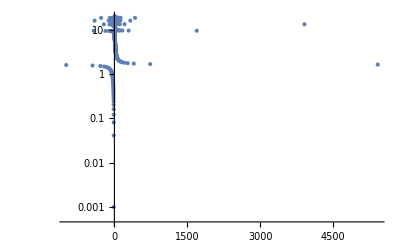

{{-12.59,-0.001},{-12.5894,-0.00104713},{-12.5888,-0.00109648},{-12.5881,-0.00114815},{-12.5873,-0.00120226},{-12.5866,-0.00125893},{-12.5858,-0.00131826},{-12.585,-0.00138038},{-12.5841,-0.00144544},{-12.5832,-0.00151356},{-12.5823,-0.00158489},{-12.5813,-0.00165959},{-12.5802,-0.0017378},{-12.5791,-0.0018197},{-12.578,-0.00190546},{-12.5768,-0.00199526},{-12.5755,-0.0020893},{-12.5742,-0.00218776},{-12.5729,-0.00229087},{-12.5714,-0.00239883},{-12.5699,-0.00251189},{-12.5684,-0.00263027},{-12.5667,-0.00275423},{-12.565,-0.00288403},{-12.5632,-0.00301995},{-12.5613,-0.00316228},{-12.5593,-0.00331131},{-12.5572,-0.00346737},{-12.5551,-0.00363078},{-12.5528,-0.00380189},{-12.5504,-0.00398107},{-12.5479,-0.00416869},{-12.5453,-0.00436516},{-12.5426,-0.00457088},{-12.5398,-0.0047863},{-12.5368,-0.00501187},{-12.5336,-0.00524807},{-12.5304,-0.00549541},{-12.5269,-0.0057544},{-12.5233,-0.0060256},{-12.5196,-0.00630957},{-12.5157,-0.00660693},{-12.5115,-0.00691831},{-12.5072,-0.00724436},{-12.5027,-0.00758578},{-12.498,-0.00794328},{-12.4931,-0.00831764},{-12.4879,-0.00870964},{-12.4825,-0.00912011},{-12.4768,-0.00954993},{-12.4709,-0.01},{-12.4647,-0.0104713},{-12.4582,-0.0109648},{-12.4514,-0.0114815},{-12.4443,-0.0120226},{-12.4368,-0.0125893},{-12.429,-0.0131826},{-12.4209,-0.0138038},{-12.4123,-0.0144544},{-12.4034,-0.0151356},{-12.3941,-0.0158489},{-12.3843,-0.0165959},{-12.3741,-0.017378},{-12.3634,-0.018197},{-12.3522,-0.0190546},{-12.3405,-0.0199526},{-12.3283,-0.020893},{-12.3155,-0.0218776},{-12.3021,-0.0229087},{-12.2881,-0.0239883},{-12.2734,-0.0251189},{-12.2581,-0.0263027},{-12.2421,-0.0275423},{-12.2254,-0.0288403},{-12.2079,-0.0301995},{-12.1896,-0.0316228},{-12.1704,-0.0331131},{-12.1504,-0.0346737},{-12.1295,-0.0363078},{-12.1077,-0.0380189},{-12.0848,-0.0398107},{-12.061,-0.0416869},{-12.036,-0.0436516},{-12.01,-0.0457088},{-11.9828,-0.047863},{-11.9544,-0.0501187},{-11.9247,-0.0524807},{-11.8937,-0.0549541},{-11.8613,-0.057544},{-11.8275,-0.060256},{-11.7922,-0.0630957},{-11.7554,-0.0660693},{-11.717,-0.0691831},{-11.6769,-0.0724436},{-11.6351,-0.0758578},{-11.5914,-0.0794328},{-11.5459,-0.0831764},{-11.4985,-0.0870964},{-11.449,-0.0912011},{-11.3975,-0.0954993},{-11.3437,-0.1},{-11.2877,-0.104713},{-11.2294,-0.109648},{-11.1687,-0.114815},{-11.1055,-0.120226},{-11.0396,-0.125893},{-10.9711,-0.131826},{-10.8999,-0.138038},{-10.8258,-0.144544},{-10.7487,-0.151356},{-10.6686,-0.158489},{-10.5853,-0.165959},{-10.4988,-0.17378},{-10.409,-0.18197},{-10.3158,-0.190546},{-10.2191,-0.199526},{-10.1187,-0.20893},{-10.0146,-0.218776},{-9.90676,-0.229087},{-9.795,-0.239883},{-9.67925,-0.251189},{-9.55942,-0.263027},{-9.43544,-0.275423},{-9.3072,-0.288403},{-9.17464,-0.301995},{-9.03767,-0.316228},{-8.89622,-0.331131},{-8.75023,-0.346737},{-8.59962,-0.363078},{-8.44433,-0.380189},{-8.28433,-0.398107},{-8.11954,-0.416869},{-7.94995,-0.436516},{-7.7755,-0.457088},{-7.59619,-0.47863},{-7.41198,-0.501187},{-7.22287,-0.524807},{-7.02886,-0.549541},{-6.82996,-0.57544},{-6.62619,-0.60256},{-6.41756,-0.630957},{-6.20413,-0.660693},{-5.98593,-0.691831},{-5.76302,-0.724436},{-5.53547,-0.758578},{-5.30335,-0.794328},{-5.06674,-0.831764},{-4.82575,-0.870964},{-4.58046,-0.912011},{-4.331,-0.954993},{-4.07749,-1.},{-3.82003,-1.04713},{-3.55878,-1.09648},{-3.29386,-1.14815},{-3.02542,-1.20226},{-2.7536,-1.25893},{-2.47855,-1.31826},{-2.20041,-1.38038},{-1.91934,-1.44544},{-1.63548,-1.51356},{-1.34898,-1.58489},{-1.05997,-1.65959},{-0.768592,-1.7378},{-0.474967,-1.8197},{0.418278,-2.0893},{0.719843,-2.18776},{1.0232,-2.29087},{1.32831,-2.39883},{1.63515,-2.51189},{1.94373,-2.63027},{2.25407,-2.75423},{2.56623,-2.88403},{2.8803,-3.01995},{3.19641,-3.16228},{3.51472,-3.31131},{3.83544,-3.46737},{4.15882,-3.63078},{4.48517,-3.80189},{4.81486,-3.98107},{5.14831,-4.16869},{5.48607,-4.36516},{5.82869,-4.57088},{6.17688,-4.7863},{6.53145,-5.01187},{6.89333,-5.24807},{7.26364,-5.49541},{7.64366,-5.7544},{8.03487,-6.0256},{8.43907,-6.30957},{8.85834,-6.60693},{9.29518,-6.91831},{9.75259,-7.24436},{10.2342,-7.58578},{10.7444,-7.94328},{11.2887,-8.31764},{11.8738,-8.70964},{12.5085,-9.12011},{13.2058,-9.54993},{13.9763,-10.},{14.8414,-10.4713},{15.8277,-10.9648},{16.9727,-11.4815},{18.3307,-12.0226},{19.9841,-12.5893},{22.0637,-13.1826},{24.7911,-13.8038},{28.5739,-14.4544},{63.4485,-16.5959},{134.724,-17.378},{-343.356,-18.197},{-68.7348,-19.0546},{-34.2089,-19.9526}}

```mathematica
ListLogPlot[taben1,PlotRange->All]
taben
```

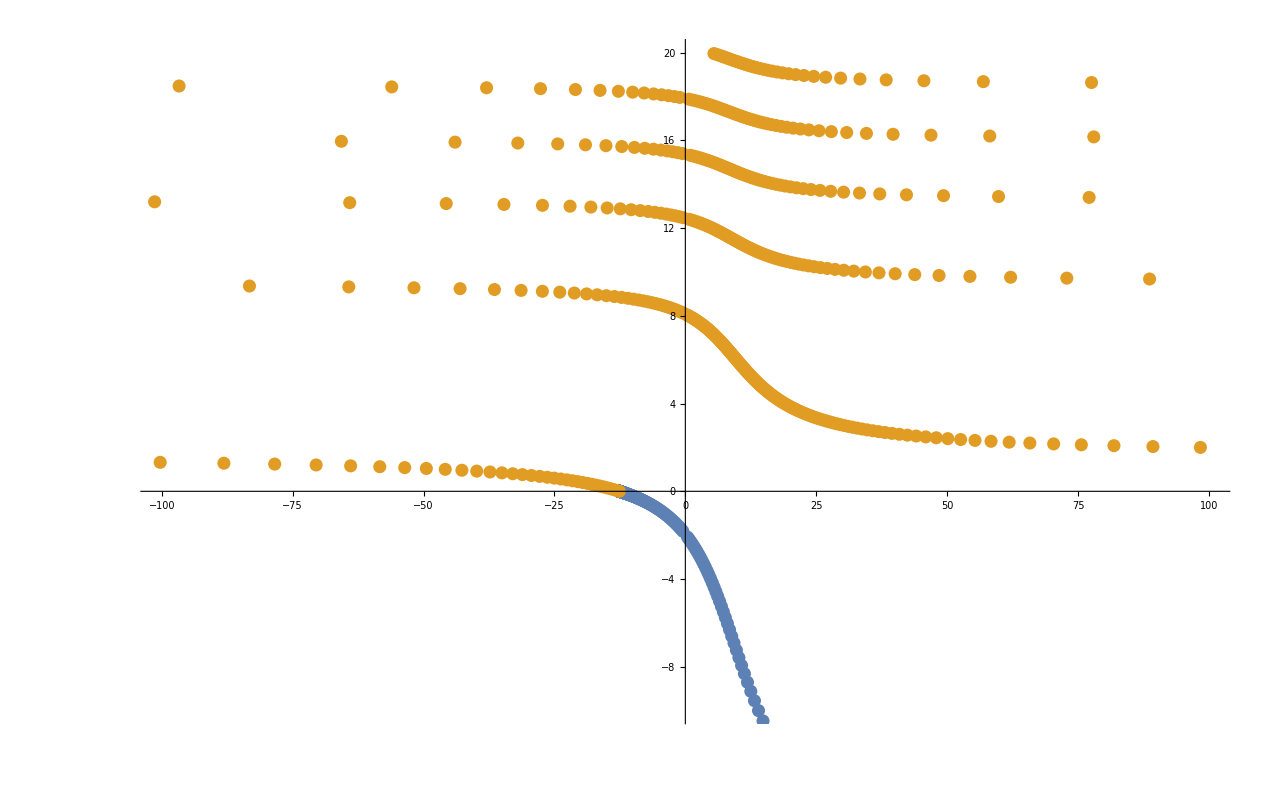

```mathematica
ListPlot[{taben,taben1},PlotRange->{{-100,100},{-10,20}}]
```

```mathematica
Export["Drop_1D_30_07.csv",Join[taben,taben1]]
```

Drop_1D_30_07.csv

```mathematica
tabb=Join[taben,taben1];
```

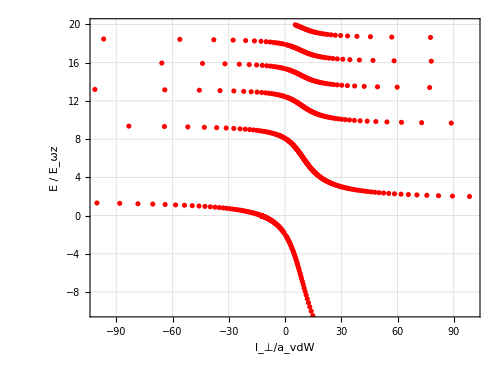

```mathematica
ListPlot[tabb,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
new=FindCurvePath[tabb.{{1,0},{0,100}}];
new1=Join[tabb[[#]]&/@new];
```

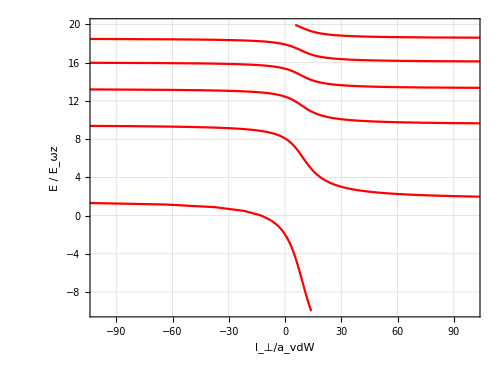

```mathematica
ListLinePlot[new1,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->Red,FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```